# Cuaderno de Prácticas

#### ALGEBRA

### Grado en Ingeniería Informática

#### CURSO 2022/23.

## Datos Personales

Nombre y apellidos : Javier Francisco Dibo Gómez
DNI: 77646884B
Grupo de teoría: A
Grupo de prácticas: 2

## Sesion 7

#### Funciones

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

Dada una matriz de adyacencia, devuelve el numero cromatico

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

Dada una matriz de adyacencia, devuelve si es plano

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

Dada una matriz de adyacencia, devuelve una coloracion optima

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

#### Ejercicio 1

-Graphics-

#### a.i.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

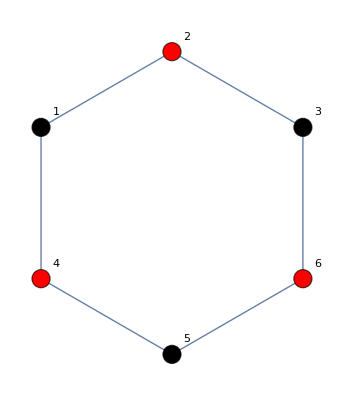

```mathematica
W={1,2,3,4,5,6};
F={1->2,2->3,3->6,6->5,5->4,4->1};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.ii.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

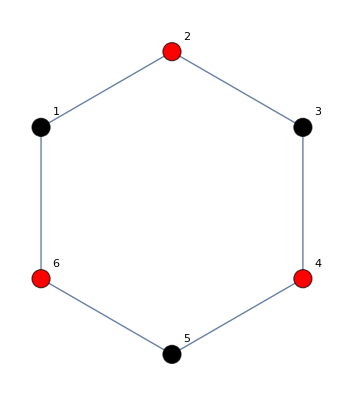

```mathematica
W={1,2,3,4,5,6};
F={1->2,2->3,3->4,4->5,5->6,6->1};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.iii.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

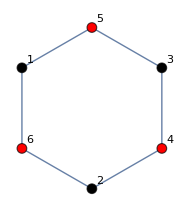

```mathematica
W={1,2,3,4,5,6};
F={1->6,2->4,3->5,4->3,5->1,6->2};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.iv.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

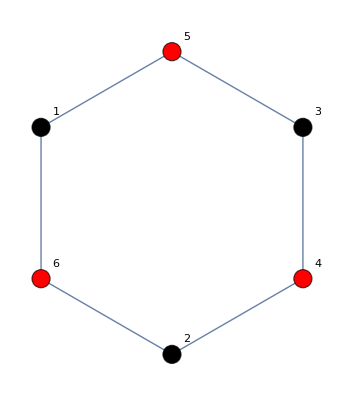

```mathematica
W={1,2,3,4,5,6};
F={1->6,2->4,3->5,4->3,5->1,6->2};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.v.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Rojo

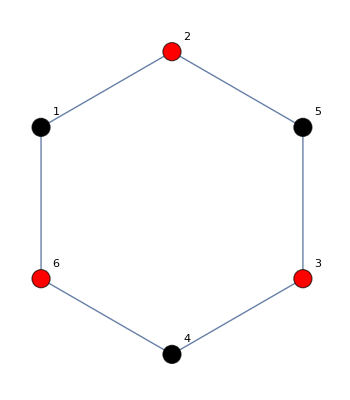

```mathematica
W={1,2,3,4,5,6};
F={1->6,2->5,3->4,1->2,3->5,4->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### a.vi.

{Numero cromatico:,3}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Verde

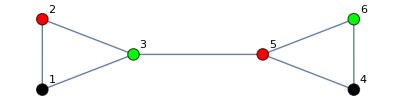

```mathematica
W={1,2,3,4,5,6};
F={1->2,1->3,2->3,3->5,4->5,4->6,5->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### octogono.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

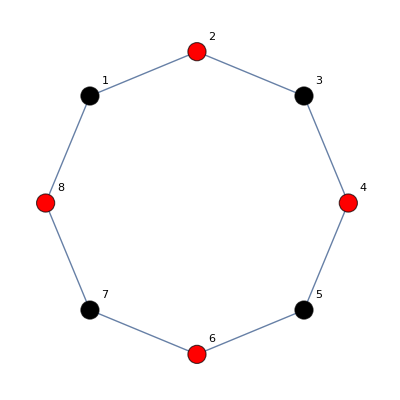

```mathematica
W={1,2,3,4,5,6,7,8};
F={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### k6.

{Numero cromatico:,6}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

Vértice 5, color Amarillo

Vértice 6, color Cyan

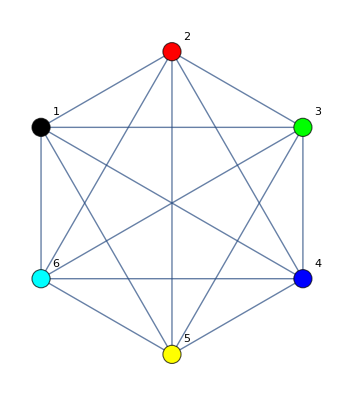

```mathematica
W={1,2,3,4,5,6};
F={2->1,3->1,4->1,5->1,6->1,1->2,3->2,4->2,5->2,6->2,1->3,2->3,4->3,5->3,6->3,1->4,2->4,3->4,5->4,6->4,
1->5,2->5,3->5,4->5,6->5,1->6,2->6,3->6,4->6,5->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### k3,3.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

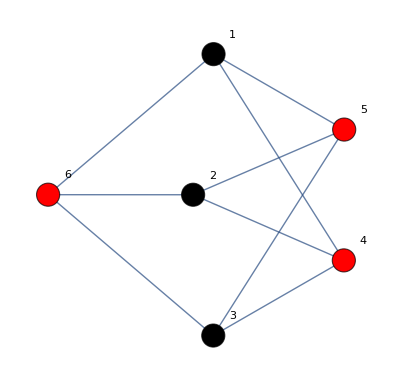

```mathematica
W={1,2,3,4,5,6};
F={1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```

#### e.

{Numero cromatico:,2}

{Plano:,True}

{Arbol:,False}

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Rojo

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Rojo

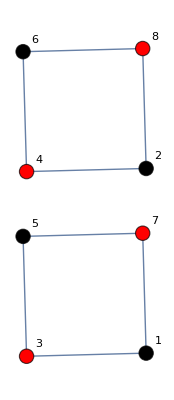

```mathematica
W={1,2,3,4,5,6,7,8};
F={1->3,1->7,2->4,2->8,3->5,4->6,5->7,6->8};
A=MATRIZADYACENCIA[W,F];
{"Numero cromatico:",NUMEROCROMATICO[A]}
{"Plano:",PLANO[A]}
{"Arbol:",ARBOL[A]}
DIBUJAR[A]
```